# 25: Eigenvalue Algorithms:

We know that we can not use the Characteristic Polynomial to compute eigenvalues. The question is how do we compute all the eigenvalues or more generally the eigen decomposition of a matrix A.

We are going to find out one way to compute roots of polynomials.

## Companion Polynomials

Matlab computes polynomial roots by building a matrix which has the same roots.  There are actually a whole bunch of these companion matrices for a given polynomial. The most common is implemented below

```mathematica
CompanionMatrix[a_]:= Module[{m=Length[a],A},
A=SparseArray[{Band[{2,1}]->1},{m-1,m-1}];
A⟦All,m-1⟧=-a⟦1;;-2⟧/a⟦-1⟧;
A
]
```

```mathematica
p[x_]:=2. x^2+3x +1 + x^7+π x^6
a=CoefficientList[p[x], x]
A=CompanionMatrix[a];
MatrixForm[A]
Sort[Eigenvalues[N[A]]]
Sort[x/.NSolve[p[x]==0,x]]
```

{1,3,2.,0,0,0,π,1}

(0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | -3
0 | 1 | 0 | 0 | 0 | 0 | -2.
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -π)

{-3.15322+0. ⅈ,-0.557703-0.0704326 ⅈ,-0.557703+0.0704326 ⅈ,-0.301024-0.891854 ⅈ,-0.301024+0.891854 ⅈ,0.864539-0.620724 ⅈ,0.864539+0.620724 ⅈ}

{-3.15322,-0.557703-0.0704326 ⅈ,-0.557703+0.0704326 ⅈ,-0.301024-0.891854 ⅈ,-0.301024+0.891854 ⅈ,0.864539-0.620724 ⅈ,0.864539+0.620724 ⅈ}

## Theorem 25.1: Galois

We all know the quadratic formula for the roots of a λ^2+b λ+c =0. There is a formula for the three roots of a cubic.  Here is one version!

```mathematica
Clear[a,b,c,λ]
λ/.Solve[λ^3+a λ^2+b λ+c==0,λ]
```

{-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}

There is a much longer formula for the four roots of a quartic

```mathematica
Clear[a,b,c,d,λ]
λ/.Solve[λ^4+a λ^3+b λ^2+c λ +d==0,λ]
```

{-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))))}

Abel proved in 1824 that no such general formula can exist for higher degree polynomials!  See Theorem 25.1 for a careful statement of the theorem. What this means is that algorithms to compute eigenvalues need to be iterative like Newton’s method!

Computing eigenvalues using the characteristic polynomial is a bad idea because it would be unstable.  But it is even worse, Abel’s result means that there is no formula for non-tiny matrices.

## Iterative Schemes

Iterative schemes have some advantages

Black-box algorithms only use the matrix rather than work on the matrix.  This is essential to exploit sparsity! It also means they do not need to compute all the eigenvalues. Maybe you only care about the big ones!

You do not have to wait for full convergence if a “rough” answer will do.

Here is another iterative eigenvalue algorithm.  The power method one very different from Jacobi: Jacobi finds all the eigenvalues by operating on the matrix while the power method finds one particular eigenvalue by using the matrix.

### Power Method: A Simple Iterative Scheme

There is a simple way to compute the eigenvector associated with the largest eigenvalue of almost any matrix A. In words, multiply by A and normalize repeatedly.  This is very easy to code.

```mathematica
PowerMethod[A_][x_]:=Module[{z=A.x},z/Norm[z]]
```

It works!  Here is a simple test on an SPD matrix.

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 0.941518 | -0.100083 | -0.669077 | -0.182837 | 0.0964034 | -0.961751 | 0.805245 | -0.655939 | -0.122598 | 0.0858145 | -0.134585 | -0.780465 | -0.898443 | -0.36096 | 0.677736 | -0.407312
2 | 0.358558 | -0.0814091 | -0.200431 | -0.199313 | 0.136971 | -0.534199 | -0.214829 | -0.382197 | -0.139167 | -0.14174 | -0.0687645 | -0.128874 | -0.382729 | -0.067244 | 0.275817 | -0.0261105
3 | 0.267836 | -0.154577 | -0.176095 | -0.20249 | 0.21069 | -0.490536 | -0.413647 | -0.40053 | -0.205311 | -0.0500292 | 0.102914 | -0.071389 | -0.362488 | 0.00991787 | 0.132543 | -0.080047
4 | 0.217788 | -0.199109 | -0.170739 | -0.149478 | 0.265972 | -0.415028 | -0.49222 | -0.374886 | -0.230499 | 0.075266 | 0.214664 | -0.0828677 | -0.323903 | 0.0678421 | -0.0332374 | -0.115133
5 | 0.190044 | -0.217272 | -0.163211 | -0.101279 | 0.287403 | -0.351455 | -0.517561 | -0.335998 | -0.233188 | 0.162824 | 0.265258 | -0.106517 | -0.282109 | 0.10557 | -0.147549 | -0.133417
6 | 0.17568 | -0.22398 | -0.157027 | -0.0704097 | 0.292028 | -0.311137 | -0.524179 | -0.305667 | -0.229707 | 0.211851 | 0.285231 | -0.124856 | -0.251284 | 0.126863 | -0.211845 | -0.142702
7 | 0.168607 | -0.226847 | -0.153292 | -0.052439 | 0.291528 | -0.288086 | -0.525757 | -0.286403 | -0.226401 | 0.237703 | 0.293013 | -0.136568 | -0.231886 | 0.138279 | -0.245903 | -0.147669
8 | 0.165212 | -0.228381 | -0.151369 | -0.042202 | 0.290121 | -0.275272 | -0.526212 | -0.275036 | -0.224399 | 0.251228 | 0.296128 | -0.143595 | -0.22039 | 0.144297 | -0.263718 | -0.150471
9 | 0.16361 | -0.229337 | -0.15051 | -0.0363785 | 0.288929 | -0.26815 | -0.526467 | -0.268503 | -0.22343 | 0.258327 | 0.297403 | -0.14772 | -0.213726 | 0.147437 | -0.273013 | -0.152108
10 | 0.16287 | -0.229968 | -0.15021 | -0.0330525 | 0.288116 | -0.26415 | -0.526688 | -0.264772 | -0.223077 | 0.262064 | 0.297924 | -0.150126 | -0.209891 | 0.149056 | -0.277845 | -0.153086
11 | 0.16254 | -0.23039 | -0.150179 | -0.0311416 | 0.287606 | -0.261867 | -0.526887 | -0.262634 | -0.223039 | 0.264028 | 0.298126 | -0.151532 | -0.207683 | 0.149876 | -0.280338 | -0.15368
12 | 0.162403 | -0.230671 | -0.150261 | -0.0300356 | 0.2873 | -0.260542 | -0.527055 | -0.261397 | -0.223137 | 0.265057 | 0.298192 | -0.152359 | -0.206407 | 0.150281 | -0.281606 | -0.154045
13 | 0.162354 | -0.230856 | -0.150378 | -0.0293899 | 0.287121 | -0.259758 | -0.52719 | -0.260672 | -0.223278 | 0.26559 | 0.298203 | -0.15285 | -0.205664 | 0.150472 | -0.282238 | -0.154272
14 | 0.162344 | -0.230979 | -0.150494 | -0.0290088 | 0.287018 | -0.259285 | -0.527294 | -0.26024 | -0.223419 | 0.265863 | 0.298192 | -0.153146 | -0.205228 | 0.150557 | -0.282542 | -0.154416
15 | 0.16235 | -0.231059 | -0.150595 | -0.0287812 | 0.286959 | -0.258993 | -0.527372 | -0.259979 | -0.223541 | 0.265999 | 0.298176 | -0.153326 | -0.204969 | 0.150589 | -0.282679 | -0.154509
16 | 0.16236 | -0.231112 | -0.150676 | -0.0286434 | 0.286925 | -0.25881 | -0.52743 | -0.259817 | -0.22364 | 0.266064 | 0.29816 | -0.153438 | -0.204813 | 0.150597 | -0.282735 | -0.15457
17 | 0.162371 | -0.231147 | -0.15074 | -0.0285588 | 0.286907 | -0.258694 | -0.527473 | -0.259716 | -0.223717 | 0.266094 | 0.298146 | -0.153508 | -0.204718 | 0.150595 | -0.282751 | -0.15461
18 | 0.16238 | -0.23117 | -0.150789 | -0.0285059 | 0.286896 | -0.258618 | -0.527503 | -0.259651 | -0.223775 | 0.266106 | 0.298135 | -0.153553 | -0.204659 | 0.150589 | -0.282751 | -0.154636
19 | 0.162388 | -0.231185 | -0.150825 | -0.0284725 | 0.28689 | -0.258568 | -0.527526 | -0.259608 | -0.223818 | 0.266109 | 0.298126 | -0.153582 | -0.204622 | 0.150582 | -0.282744 | -0.154655
20 | 0.162394 | -0.231196 | -0.150851 | -0.0284509 | 0.286886 | -0.258534 | -0.527541 | -0.25958 | -0.223849 | 0.266109 | 0.29812 | -0.153601 | -0.204598 | 0.150576 | -0.282735 | -0.154667
21 | 0.162398 | -0.231203 | -0.15087 | -0.0284368 | 0.286884 | -0.258512 | -0.527553 | -0.259561 | -0.223872 | 0.266107 | 0.298115 | -0.153614 | -0.204582 | 0.150571 | -0.282727 | -0.154675
22 | 0.162402 | -0.231207 | -0.150884 | -0.0284275 | 0.286883 | -0.258496 | -0.527561 | -0.259549 | -0.223889 | 0.266105 | 0.298112 | -0.153622 | -0.204572 | 0.150567 | -0.282721 | -0.154681
23 | 0.162404 | -0.231211 | -0.150894 | -0.0284213 | 0.286883 | -0.258486 | -0.527567 | -0.25954 | -0.2239 | 0.266103 | 0.29811 | -0.153628 | -0.204566 | 0.150564 | -0.282715 | -0.154685
24 | 0.162406 | -0.231213 | -0.150901 | -0.0284171 | 0.286882 | -0.258478 | -0.527571 | -0.259534 | -0.223909 | 0.266102 | 0.298108 | -0.153632 | -0.204561 | 0.150562 | -0.282711 | -0.154688
25 | 0.162407 | -0.231214 | -0.150907 | -0.0284142 | 0.286882 | -0.258473 | -0.527574 | -0.25953 | -0.223915 | 0.2661 | 0.298107 | -0.153635 | -0.204558 | 0.15056 | -0.282708 | -0.15469
26 | 0.162408 | -0.231215 | -0.15091 | -0.0284123 | 0.286882 | -0.25847 | -0.527576 | -0.259527 | -0.223919 | 0.2661 | 0.298106 | -0.153637 | -0.204556 | 0.150559 | -0.282706 | -0.154692
27 | 0.162409 | -0.231216 | -0.150913 | -0.0284109 | 0.286882 | -0.258467 | -0.527577 | -0.259525 | -0.223922 | 0.266099 | 0.298105 | -0.153638 | -0.204554 | 0.150558 | -0.282704 | -0.154693
28 | 0.162409 | -0.231217 | -0.150915 | -0.0284099 | 0.286882 | -0.258466 | -0.527578 | -0.259524 | -0.223925 | 0.266098 | 0.298105 | -0.153639 | -0.204553 | 0.150558 | -0.282703 | -0.154693
29 | 0.162409 | -0.231217 | -0.150916 | -0.0284093 | 0.286882 | -0.258464 | -0.527579 | -0.259523 | -0.223926 | 0.266098 | 0.298104 | -0.15364 | -0.204553 | 0.150557 | -0.282702 | -0.154694
30 | 0.16241 | -0.231217 | -0.150917 | -0.0284088 | 0.286882 | -0.258463 | -0.527579 | -0.259522 | -0.223927 | 0.266098 | 0.298104 | -0.15364 | -0.204552 | 0.150557 | -0.282702 | -0.154694
31 | 0.16241 | -0.231218 | -0.150918 | -0.0284085 | 0.286882 | -0.258463 | -0.52758 | -0.259522 | -0.223928 | 0.266097 | 0.298104 | -0.15364 | -0.204552 | 0.150557 | -0.282701 | -0.154694
32 | 0.16241 | -0.231218 | -0.150918 | -0.0284083 | 0.286882 | -0.258462 | -0.52758 | -0.259521 | -0.223928 | 0.266097 | 0.298104 | -0.153641 | -0.204552 | 0.150556 | -0.282701 | -0.154695
33 | 0.16241 | -0.231218 | -0.150918 | -0.0284081 | 0.286882 | -0.258462 | -0.52758 | -0.259521 | -0.223929 | 0.266097 | 0.298104 | -0.153641 | -0.204552 | 0.150556 | -0.282701 | -0.154695
34 | 0.16241 | -0.231218 | -0.150919 | -0.028408 | 0.286882 | -0.258462 | -0.52758 | -0.259521 | -0.223929 | 0.266097 | 0.298104 | -0.153641 | -0.204551 | 0.150556 | -0.282701 | -0.154695
35 | 0.16241 | -0.231218 | -0.150919 | -0.0284079 | 0.286882 | -0.258462 | -0.52758 | -0.259521 | -0.223929 | 0.266097 | 0.298104 | -0.153641 | -0.204551 | 0.150556 | -0.2827 | -0.154695

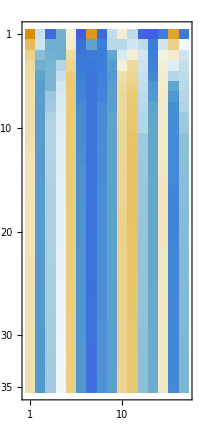

```mathematica
m=16;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic]
MatrixPlot[PowerMethodData]
```

It has almost converged to the eigenvector associated with the largest eigenvalue!

```mathematica
{{λ},{v}}=Eigensystem[A,1]
```

{{18.7827},{{-0.16241,0.231218,0.150919,0.0284077,-0.286882,0.258461,0.527581,0.25952,0.22393,-0.266097,-0.298104,0.153641,0.204551,-0.150556,0.2827,0.154695}}}

```mathematica
vv=PowerMethodData⟦-1⟧
(A.vv)/vv
```

{0.16241,-0.231218,-0.150919,-0.0284079,0.286882,-0.258462,-0.52758,-0.259521,-0.223929,0.266097,0.298104,-0.153641,-0.204551,0.150556,-0.2827,-0.154695}

```mathematica
{18.782680833027204,18.78267992377554,18.782691955769128,18.782640469938702,18.782677319405842,18.78266970926498,18.782679702106222,18.782671252773063,18.782688903488058,18.782674831333594,18.78267562671868,18.782684167730785,18.78267199699047,18.782672394627376,18.78267214569421,18.782682632835648}
```

It also works more generally! Here it is on a general symmetric matrix.

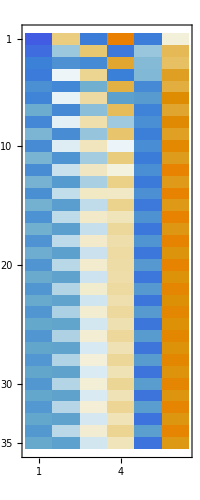

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

It also frequently (but not always) works on a general matrix.

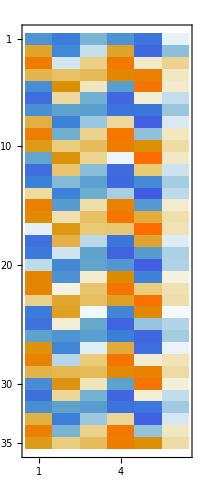

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

```mathematica
Eigenvalues[A]
```

{0.756165+1.19174 ⅈ,0.756165-1.19174 ⅈ,-0.559457+0.424853 ⅈ,-0.559457-0.424853 ⅈ,-0.0365635+0.515306 ⅈ,-0.0365635-0.515306 ⅈ}

```mathematica
vEnd=PowerMethodData⟦-3;;-1⟧
```

{{0.327082,-0.493079,-0.114887,0.137063,-0.7846,-0.0480398},{0.651219,-0.182544,0.161783,0.704838,-0.123332,0.0664067},{0.443658,0.19969,0.268569,0.655334,0.499389,0.110951}}

## Preliminary Hessenberg Reduction

For now we are going to look at classical dense matrix eigenvalue algorithms which start with a reduction very similar to a QR decomposition and then iterates to reveal all the eigenvalues of a dense matrix.

We are going to look and see what the first step does before we learn how to do it!

### Symmetric Matrix⟶Tri-Diagonal⟶^(k→∞)Diagonal

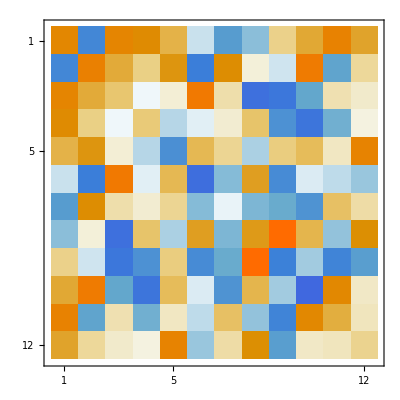
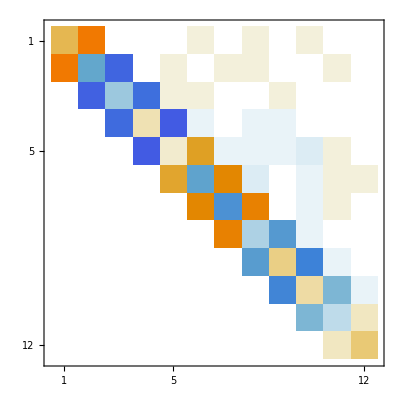
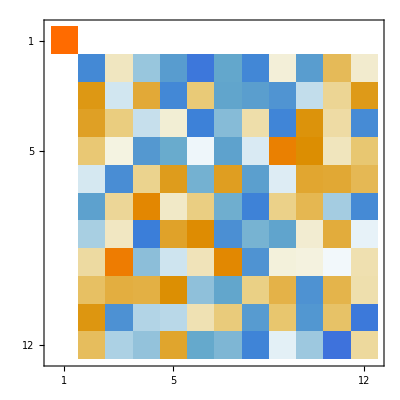

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,T}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,T,Q}]
```

```mathematica
Norm[T-Qᵀ.A.Q]
Norm[Eigenvalues[A]-Eigenvalues[T]]
```

2.1193×10^-15

1.41866×10^-14

```mathematica
TabView[{"A"->GershgorignPic[A],"T"->GershgorignPic[T]}]
```

12

The tridiagonal matrix give tighter bounds. If we could make it more diagonal we would be able to isolate the eigenvalues.  This is the plan.  For symmetric matrices we are going to work out how to make the tridiagonal matrix more diagonal.

### General Matrix⟶Almost Upper Triangular⟶^(k→∞)UT

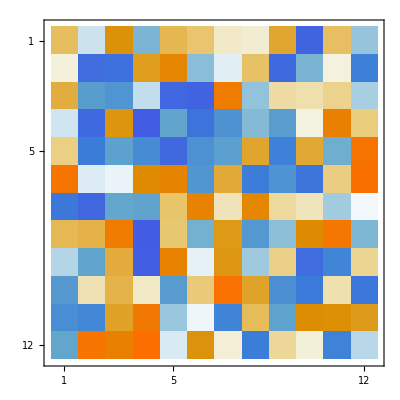
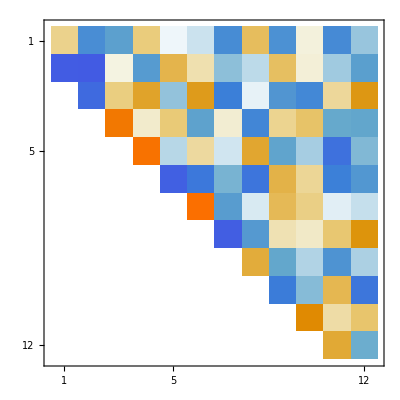
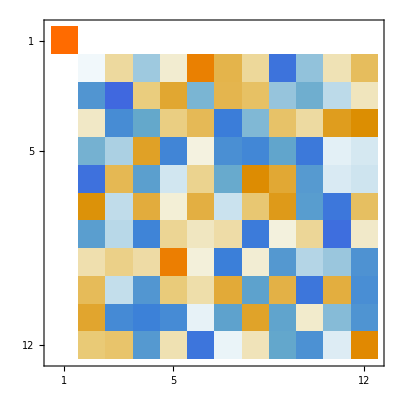

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; 
{Q,H}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,H,Q}]
```

```mathematica
Norm[H-Qᵀ.A.Q]
Norm[A-Q.H.Qᵀ]
```

1.73713×10^-15

2.48528×10^-15

```mathematica
TabView[{"A"->GershgorignPic[A],"H"->GershgorignPic[H]}]
```

12

The almost upper triangular matrix give tighter bounds. If we could make it more upper triangular we would be able to isolate the eigenvalues.  This is the plan.  For general matrices we are going to work out how to make the almost upper triangular matrix more upper triangular.

## Localization Pic Code (From Earlier)

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r1,r2},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```